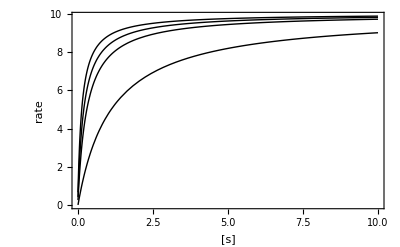

```mathematica
Plot[Table[((Vmaxf*s)/Ks(1-p/(s*Keq)))/(1+s/Ks+p/Kp)/.Vmaxf->10/.Ks->0.1/.Kp->0.75/.Keq->1000, {p,{0.25,0.75,1.5,7.5}}],{s,0.01,10}, PlotRange->All, Frame->True, FrameLabel->{"[s]","rate"}, PlotStyle->{Black, Thick}]
```

```mathematica
Table[Solve[((Vmaxf*s)/Ks(1-p/(s*Keq)))/(1+s/Ks+p/Kp)==0/.Vmaxf->10/.Ks->0.1/.Kp->0.75/.Keq->1000/.p->i ,s],{i,{0.25,0.75,1.5,7.5}}]
```

{{{s→0.00025}},{{s→0.00075}},{{s→0.0015}},{{s→0.0075}}}